```mathematica
(*Define subscripted symbols*)
Notation`AutoLoadNotationPalette=False;
<<Notation`;
Symbolize/@{Subscript[D, e],Subscript[r, e],Subscript[r, 0],Subscript[r, f]};
```

#### Importing Data

```mathematica
(*Importing Dataset of Spectroscopic Constants*)
SetDirectory[NotebookDirectory[]];
molecularData=Import["molecular_data.csv", {"CSV","Dataset"},"HeaderLines"->{1,1}]
```

#### Parameters

```mathematica
(*Molecular Constants*)
molecule = "H2";
{Subscript[D, e],Subscript[r, e],μ,α}={"D_e","r_e","mu","alpha"}/.Normal[molecularData[molecule]];
μ=μ*931.49410372*10^6; (*amu to eV/c^2*)
ℏ=1973.269804;

ℓ = 25;
Subscript[r, 0] =0.01; Subscript[r, f]= 10;
gridPoints = 2000;
```

#### The Finite Difference Method

```mathematica
(*Discretize r-grid*)
step =(Subscript[r, f]-Subscript[r, 0])/gridPoints;
rVals =Array[#&,gridPoints,{Subscript[r, 0],Subscript[r, f]}];

(*Define Potential Function (with Centrifugal Term)*)
ModifiedMorse[r_]:=Subscript[D, e] ⅇ^(-2α(r-Subscript[r, e])/Subscript[r, e])-2 Subscript[D, e] ⅇ^(-α(r-Subscript[r, e])/Subscript[r, e])+ℏ^2/(2μ)(ℓ(ℓ+1))/r^2;

(*Potential Energy Matrix*)
𝒱=DiagonalMatrix[ModifiedMorse[rVals]];
(*Kinetic Energy Matrix*)
𝒦=-ℏ^2/(2μ step^2)(DiagonalMatrix[ConstantArray[-2,gridPoints]]+DiagonalMatrix[ConstantArray[1,gridPoints-1],-1]+DiagonalMatrix[ConstantArray[1,gridPoints-1],1]);
(*Hamiltonian Matrix*)
ℋ=𝒦+𝒱;

(*Diagonalize Hamiltonian Matrix*)
{energyVals,eigenFunctions} =Eigensystem[ℋ]//Quiet;
(*Sort Eigenvalues/Eigenfunctions by Most Negative Eigenvalues*)
energyPos = Ordering[energyVals];
energyVals=energyVals[[energyPos]];
eigenFunctions=eigenFunctions[[energyPos]];
```

#### Eigenvalues and Eigenfunctions

```mathematica
NumberForm[-#,{20,8}]&/@ energyVals[[{1,4,6}]]//TableForm
```

1.16592194
0.34028050
-0.01980385

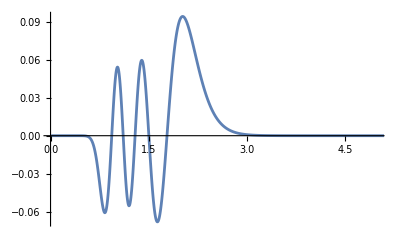

```mathematica
ListLinePlot[Thread[{rVals,eigenFunctions[[6]]}], PlotRange->{{0,5},Full}]
```

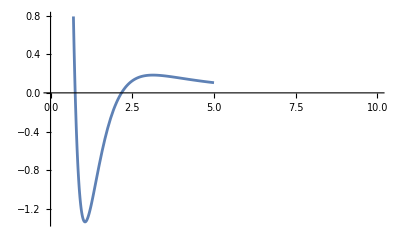

```mathematica
Plot[ModifiedMorse[r],{r,0.7,5},PlotRange->{{0,10},Full}]
```